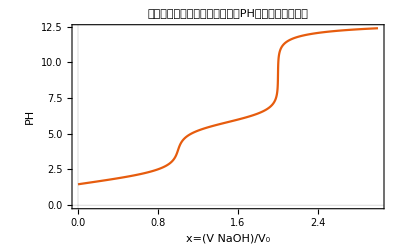

```mathematica
k1=1.8*10^-2;                                                                                                                     
 k2=1.5*10^-6;object=Table[{x,NSolve[{H+(0.1x)/(1+x)==0.1/(1+x)*(H*k1+2*k1*k2)/(H^2+k1*H+k1*k2)+10^-14/H,PH==-Log10[H],H>0},{H,PH},Reals][[1,2,2]]},{x,0,3,0.001}];
figure=ListLinePlot[object,PlotRange->Full,PlotTheme->"Scientific",FrameLabel->{{HoldForm[PH],None},{HoldForm[x=(V(NaOH))/Subscript[V, 0]],None}},PlotLabel->HoldForm[用氢氧化钠滴定顺丁烯二酸溶液PH随滴定进程变化图],LabelStyle->{18,GrayLevel[0]},ImageSize->Full]
```

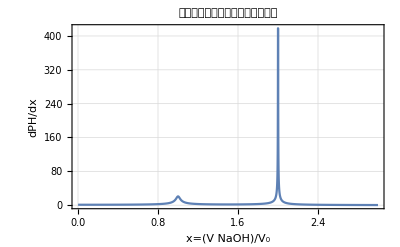

```mathematica
y=Table[object[[i,2]],{i,1,Length[object]}];
dx=object[[2,1]];
diffrential=Table[{i*dx,(y[[i+1]]-y[[i]])/dx},{i,1,Length[object]-1}];
ListLinePlot[diffrential,PlotTheme->"Detailed",FrameLabel->{{HoldForm[dPH/dx],None},{HoldForm[x=(V(NaOH))/Subscript[V, 0]],None}},PlotRange->Full,PlotLabel->HoldForm[滴定曲线的差分随滴定进程变化图],LabelStyle->{18,GrayLevel[0]},ImageSize->Full]
```

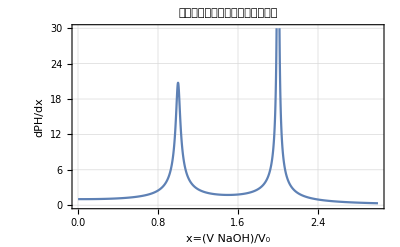

```mathematica
ListLinePlot[diffrential,PlotTheme->"Detailed",FrameLabel->{{HoldForm[dPH/dx],None},{HoldForm[x=(V(NaOH))/Subscript[V, 0]],None}},PlotRange->{{0,3},{0,30}},PlotLabel->HoldForm[滴定曲线的差分随滴定进程变化图],LabelStyle->{18,GrayLevel[0]},ImageSize->Full]
```

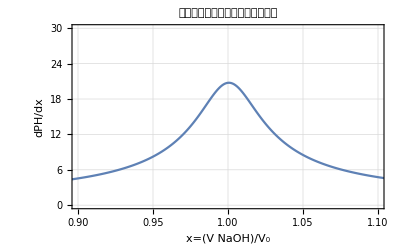

```mathematica
ListLinePlot[diffrential,PlotTheme->"Detailed",FrameLabel->{{HoldForm[dPH/dx],None},{HoldForm[x=(V(NaOH))/Subscript[V, 0]],None}},PlotRange->{{0.9,1.1},{0,30}},PlotLabel->HoldForm[滴定曲线的差分随滴定进程变化图],LabelStyle->{18,GrayLevel[0]},ImageSize->Full]
```

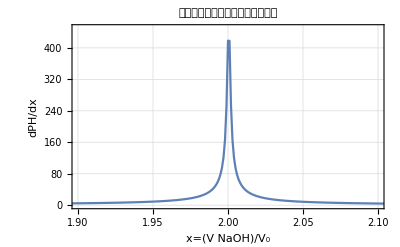

```mathematica
ListLinePlot[diffrential,PlotTheme->"Detailed",FrameLabel->{{HoldForm[dPH/dx],None},{HoldForm[x=(V(NaOH))/Subscript[V, 0]],None}},PlotRange->{{1.9,2.1},{0,450}},PlotLabel->HoldForm[滴定曲线的差分随滴定进程变化图],LabelStyle->{18,GrayLevel[0]},ImageSize->Full]
```

```mathematica
jump1=-NSolve[{H+(0.1x)/(1+x)==0.1/(1+x)*(H*k1+2*k1*k2)/(H^2+k1*H+k1*k2)+10^-14/H,PH==-Log10[H],x==0.999,H>0},{H,PH,x},Reals][[1,3,2]]+NSolve[{H+(0.1x)/(1+x)==0.1/(1+x)*(H*k1+2*k1*k2)/(H^2+k1*H+k1*k2)+10^-14/H,PH==-Log10[H],x==1.001,H>0},{H,PH,x},Reals][[1,3,2]]
(*第一次滴定突跃jump1*)
jump2=-NSolve[{H+(0.1x)/(1+x)==0.1/(1+x)*(H*k1+2*k1*k2)/(H^2+k1*H+k1*k2)+10^-14/H,PH==-Log10[H],x==1.998,H>0},{H,PH,x},Reals][[1,3,2]]+NSolve[{H+(0.1x)/(1+x)==0.1/(1+x)*(H*k1+2*k1*k2)/(H^2+k1*H+k1*k2)+10^-14/H,PH==-Log10[H],x==2.002,H>0},{H,PH,x},Reals][[1,3,2]]
(*第二次滴定突跃jump2*)
```

0.0415065

1.34208